# Temas de física 4: PC2

Ariadna Uxue Palomino Ylla									20161343

```mathematica
ClearAll["Global`*"]
```

## Definiendo funciones para graficar las singularidades, los retratos de fase y otras cosas para el análisis cualitativo

```mathematica
LinCam[f_,g_,n_:3]:=StreamDensityPlot[{f[x,y],g[x,y]},{x,-1*n,n},{y,-1*n,n},ColorFunction->"LightTerrain",StreamStyle->Darker[Brown]];(*Esta función grafica los stramlines*)
```

```mathematica
Singularidades[f_,g_]:=Solve[{f[x,y]==0,g[x,y]==0}](*Esta función devuelve las singularidades*)
```

```mathematica
Points[f_,g_]:=Graphics[{PointSize[0.015],Yellow,Point[Table[{x,y}/.Select[Singularidades[f,g],FreeQ[#,Complex]&][[i]],{i,Dimensions[Select[Singularidades[f,g],FreeQ[#,Complex]&]][[1]]}]]}](*Esta función grafica los puntos de las singularidades*)
```

```mathematica
Showing[g1_,g2_,g3___]:=Show[{g1,g2,g3},PlotRange->{{-10,10},{-10,10}},AxesLabel->{"x",HoldForm["y"]},PlotLabel->HoldForm["Sistema no lineal"],Axes->True,Frame->True,ImageSize->{1000,1000},AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->18,FontColor->RGBColor[0,0,0.4]}] (*Esta función muestra los plots*)
```

```mathematica
ode[f_,g_,x0_,y0_,ti_,tf_:10]:=NDSolve[{x'[t]==f[x[t],y[t]],y'[t]==g[x[t],y[t]],x[0]==x0,y[0]==y0},{x[t],y[t]},{t,ti,tf},MaxSteps->Infinity];(*Esta función produce una sola solución*)
```

```mathematica
p[f_,g_,x0_,y0_,ti_,tf_:10]:=ParametricPlot[Evaluate[Table[{x[t],y[t]}/.ode[f,g,x0,y0,ti,tf]],{t,ti,tf},PlotStyle->White, PlotRange->{{-3,3},{-3,3}},PlotPoints->1000,AxesLabel->{"x","y"}]];(*Esta función grafica una solución*)
```

```mathematica
JacMatrix[f_,g_]:={{D[f[x,y],x],D[f[x,y],y]},{D[g[x,y],x],D[g[x,y],y]}}//MatrixForm;(*Esta función devuelve la matriz Jacobiana*)
```

```mathematica
Jac[f_,g_]:={{D[f[x,y],x],D[f[x,y],y]},{D[g[x,y],x],D[g[x,y],y]}};(*Esta función devuelve lo anterior pero no en forma de matriz*)
```

Pregunta 2 : Determinar las singularidades, analizarlas en forma cualitativa y establecer el retrato de    fase

Piecewise[{{ẋ, =2-x-y^2}, {ẏ, =-y(x^2+y^2-3x+1)}}]

Definiendo las funciones componentes del campo vectorial asociado al sistema:

```mathematica
f1[x_,y_]=2-x-y^2;
g1[x_,y_]=-y*(x^2+y^2-3x+1);
```

Ubicando las singularidades:

```mathematica
Singularidades[f1,g1]
```

{{x→1,y→-1},{x→2,y→0},{x→3,y→-ⅈ},{x→3,y→ⅈ},{x→1,y→1}}

En este caso hay 3 singularidades que pueden ser representadas en el retrato de fase (P1,P2,P3 respectivamente). 
Estableciendo la matriz Jacobiana:

```mathematica
J1=JacMatrix[f1,g1]
```

(-1 | -2 y
-(-3+2 x) y | -1+3 x-x^2-3 y^2)

Analizando la primera singularidad P1=(1,-1):

Evaluando la matriz Jacobiana en P1:

```mathematica
M11=J1/. Singularidades[f1,g1][[1]]//MatrixForm
```

(-1 | 2
-1 | -2)

Obteniendo los autovalores:

```mathematica
Jac[f1,g1]/. Singularidades[f1,g1][[1]]//Eigenvalues
```

{1/2 (-3+ⅈ √7),1/2 (-3-ⅈ √7)}

Son autovalores complejos conjugados con parte real diferente a cero; por lo cual, es un punto singular hiperbolico y se puede aplicar el teorema de Hartman. Esta singularidad  tiene un comportamiento cualitativo de tipo “foco espiral estable”.

Analizando la segunda singularidad P2=(2,0):

Evaluando la matriz Jacobiana en P2:

```mathematica
M12=J1/. Singularidades[f1,g1][[2]]//MatrixForm
```

(-1 | 0
0 | 1)

Obteniendo los autovalores:

```mathematica
Jac[f1,g1]/. Singularidades[f1,g1][[2]]//Eigensystem
```

{{-1,1},{{1,0},{0,1}}}

Son autovalores reales diferentes a cero; por lo cual, es un punto singular hiperbolico y se puede aplicar el teorema de Hartman. Esta singularidad  tiene un comportamiento cualitativo de tipo “ensilladura”.

Analizando la primera singularidad P3=(1,1):

Evaluando la matriz Jacobiana en P3:

```mathematica
M13=J1/. Singularidades[f1,g1][[5]]//MatrixForm
```

(-1 | -2
1 | -2)

Obteniendo los autovalores:

```mathematica
Jac[f1,g1]/. Singularidades[f1,g1][[5]]//Eigenvalues
```

{1/2 (-3+ⅈ √7),1/2 (-3-ⅈ √7)}

Son autovalores complejos conjugados con parte real diferente a cero; por lo cual, es un punto singular hiperbolico y se puede aplicar el teorema de Hartman. Esta singularidad  tiene un comportamiento cualitativo de tipo “foco espiral estable”

```mathematica
P1=Points[f1,g1];(*Graficando los puntos de las singularidades*)
```

```mathematica
l1=LinCam[f1,g1,10]; (*Graficando lineas de corriente Streamlines*)
```

```mathematica
G1={p[f1,g1,0,-3.1,-0.05085382233136243],p[f1,g1,0,-1.5,-0.19339146404625434],p[f1,g1,0.1,0.1,-0.768],p[f1,g1,0,3.1,-0.05],p[f1,g1,-0.1,-0.1,-0.678265],p[f1,g1,0,1.5,-0.19],p[f1,g1,-7,6,-0.007793515888580394],p[f1,g1,7,-6,-0.007793515888580394],p[f1,g1,3,3, -0.05041075641153548]};(*Retrato de fase del sistema considerando 9 curvas solución*)
```

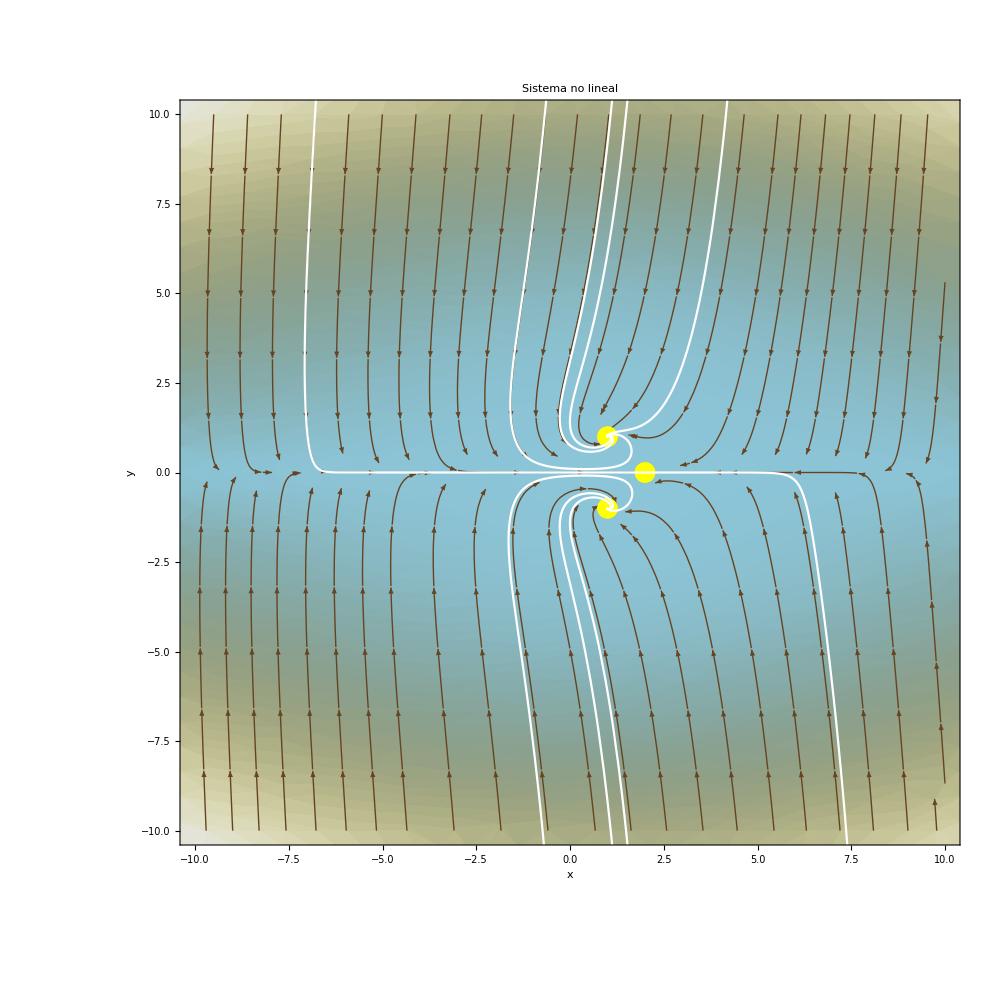

```mathematica
Showing[l1,P1,G1](*Muestra los gráficos*)
```

Pregunta 3 : Determinar las singularidades, analizarlas en forma cualitativa y establecer el retrato de    fase

Piecewise[{{ẋ, =x}, {ẏ, =x^2+y^2-1}}]

Definiendo las funciones componentes del campo vectorial asociado al sistema:

```mathematica
f2[x_,y_]=x;
g2[x_,y_]=x^2+y^2-1;
```

Ubicando las singularidades:

```mathematica
Singularidades[f2,g2]
```

{{x→0,y→-1},{x→0,y→1}}

En este caso hay 2 singularidades que pueden ser representadas en el retrato de fase (P1 y P2 respectivamente). 
Estableciendo la matriz Jacobiana:

```mathematica
J2=JacMatrix[f2,g2]
```

(1 | 0
2 x | 2 y)

Analizando la primera estabilidad P1=(0,-1):

Evaluando la matriz Jacobiana en P1:

```mathematica
M21=J2/. Singularidades[f2,g2][[1]]//MatrixForm
```

(1 | 0
0 | -2)

Obteniendo los autovalores:

```mathematica
Jac[f2,g2]/. Singularidades[f2,g2][[1]]//Eigensystem
```

{{-2,1},{{0,1},{1,0}}}

Son autovalores reales diferentes a cero; por lo cual, es un punto singular hiperbolico y se puede aplicar el teorema de Hartman. Esta singularidad  tiene un comportamiento cualitativo de tipo “ensilladura”

Analizando la segunda singularidad P2=(0,1):

Evaluando la matriz Jacobiana en P2:

```mathematica
M22=J2/. Singularidades[f2,g2][[2]]//MatrixForm
```

(1 | 0
0 | 2)

Obteniendo los autovalores:

```mathematica
Jac[f2,g2]/. Singularidades[f2,g2][[2]]//Eigensystem
```

{{2,1},{{0,1},{1,0}}}

Son autovalores reales diferentes a cero; por lo cual, es un punto singular hiperbolico y se puede aplicar el teorema de Hartman. Esta singularidad  tiene un comportamiento cualitativo de tipo “nodo inestable”

```mathematica
P2=Points[f2,g2];(*Graficando los puntos de las singularidades*)
```

```mathematica
l2=LinCam[f2,g2,10];(*Graficando lineas de corriente Streamlines*)
```

```mathematica
G2={p[f2,g2,1,-3.1,-0.32419470391253862, 1.4217500472897294],p[f2,g2,-1,-3.1,-0.32419470391253862, 1.4217500472897294],p[f2,g2,0.1,0.1,-20,3.6433030168016346],p[f2,g2,1,3.1,-20,0.32054941131929514],p[f2,g2,-1,3.1,-20,0.32054941131929514],p[f2,g2,-0.1,-0.1,-20, 3.644170027972075],p[f2,g2,-5,6,-0.6837597090116763,0.13822836115174135],p[f2,g2,5,6,-0.6837597090116763,0.13822836115174135]};(*Retrato de fase del sistema considerando 8 curvas solución*)
```

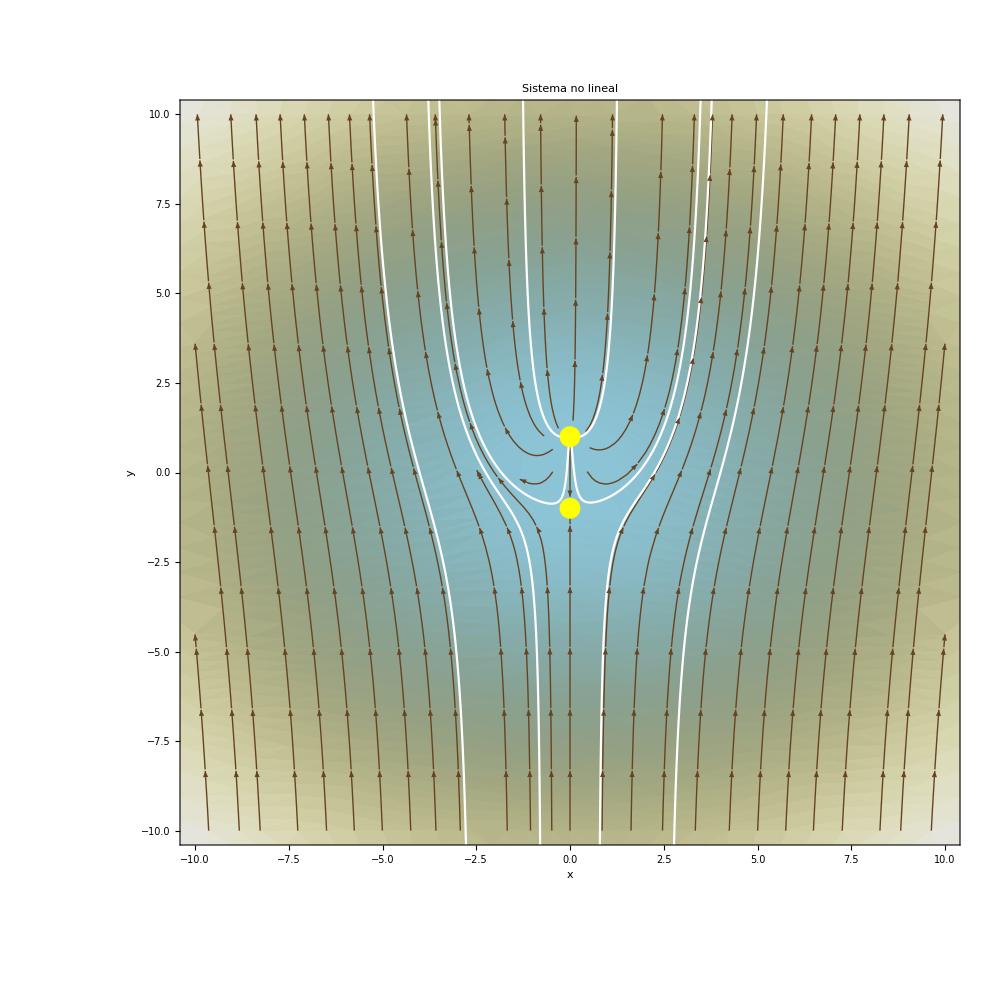

```mathematica
Showing[l2,P2,G2](*Muestra los gráficos*)
```